### Load local GeoJSON data

```mathematica
file=Import["E:\\amomorning\\Desktop\\wien.geojson","JSON"]
```

{type→FeatureCollection,features→{{type→Feature,geometry→{type→Polygon,coordinates→{{{16.1818,48.1711},{16.1819,48.171},{16.1829,48.1698},{16.184,48.1693},{16.1842,48.1692},{16.1846,48.1689},{16.1877,48.1681},{16.1937,48.1664},{16.1962,48.164},{16.1974,48.1609},{16.1967,48.1566},{16.198,48.1545},{16.1982,48.1541},2351,{16.2039,48.194},{16.2039,48.1939},{16.2031,48.1909},{16.1998,48.1862},{16.1959,48.1838},{16.1932,48.1806},{16.1902,48.1789},{16.1891,48.1782},{16.1878,48.1771},{16.1876,48.1739},{16.1872,48.1736},{16.1818,48.1711}}}},properties→{osm_id→-109166,admin_level→4,parents→-16239,name→Vienna,local_name→Wien,name_en→Vienna}}}}
 |  |  |  |

```mathematica
coords=Flatten[file[[2,2,1,2,2,2,2]],1]
```

{{16.1818,48.1711},{16.1819,48.171},{16.1829,48.1698},{16.184,48.1693},{16.1842,48.1692},{16.1846,48.1689},{16.1877,48.1681},{16.1937,48.1664},{16.1962,48.164},{16.1974,48.1609},{16.1967,48.1566},{16.198,48.1545},{16.1982,48.1541},{16.2014,48.1548},{16.2035,48.1555},{16.2232,48.1532},{16.2232,48.1527},{16.2234,48.1526},2340,{16.2069,48.2025},{16.2074,48.2023},{16.2059,48.1997},{16.2057,48.1991},{16.2053,48.1977},{16.204,48.1964},{16.2039,48.194},{16.2039,48.1939},{16.2031,48.1909},{16.1998,48.1862},{16.1959,48.1838},{16.1932,48.1806},{16.1902,48.1789},{16.1891,48.1782},{16.1878,48.1771},{16.1876,48.1739},{16.1872,48.1736},{16.1818,48.1711}}
 |  |  |  |

Polygon[…]

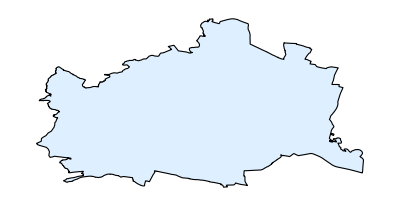

```mathematica
ply=Polygon[coords]
Graphics[{EdgeForm[Black],LightBlue, ply}]
```

```mathematica
ToWKT[coords_List, type_String]:=Module[{},type<>"(("
<> StringTake[ToString[Table[ToString[coords[[ n,1]]]<>" "<>ToString[coords[[n,2]]],{n,Length@coords}]],{2,-2}] <>"))"
]
```

```mathematica
FromWKT[geom_String]:=Polygon[ToExpression[StringSplit[StringSplit[StringSplit[geom,{"((","))"}][[2]],","]," "]]]
```

```mathematica
wkt=ToWKT[Flatten[file[[2,2,1,2,2,2,2]],1],"POLYGON"];
```

```mathematica
FromWKT[wkt]
```

Polygon[…]

### Open a connection to database

```mathematica
Needs["DatabaseLink`"]
$DB = OpenSQLConnection[JDBC["PostgreSQL", "ip:port:database"], "Username" -> "user", "Password" -> "password"]
```

SQLConnection[…]

```mathematica
SQLTables[$DB]
```

{SQLTable[blocks,TableType→TABLE],SQLTable[buildings,TableType→TABLE],SQLTable[city,TableType→TABLE],SQLTable[functions,TableType→TABLE],SQLTable[roads,TableType→TABLE],SQLTable[spatial_ref_sys,TableType→TABLE]}

{Polygon[…]}

### Insert Data

```mathematica
geodata="ST_GeomFromText('"<>wkt<>"')";
```

```mathematica
res=SQLExecute[$DB,"Update city set boundary = "<>geodata<>" where name='wien'"];
```

### Query Data

```mathematica
boundaryRes=SQLExecute[$DB,"select name, ST_asGeoJSON(ST_Transform(boundary,3785))
from city"];
```

```mathematica
boundary=Table[Polygon[ImportString[res[[n,2]],"JSON"][[3,2]]],{n,Length@boundaryRes}]
```

{Polygon[…]}

```mathematica
res=SQLExecute[$DB,"select blocks.id, ST_asGeoJSON(ST_Transform(blocks.geom,3785))
from city, blocks
where city.name='wien' and st_contains(city.boundary, blocks.geom)"];
```

```mathematica
blocks=Table[Polygon[ImportString[res[[n,2]],"JSON"][[3,2]]],{n,Length@res}];
```

```mathematica
Length@blocks
```

6901

```mathematica
blocks[[1;;10]]
```

{Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…]}

```mathematica
blocks[[10;;20]]
```

{Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…]}

### Problem logs:

1.  PolygonCoordinates returns sorted coordinates.

```mathematica
ToWKTerror[ply_Polygon]:=Module[{coords},coords=PolygonCoordinates[ply];
"POLYGON (" <> StringTake[ToString[Table[ToString[coords[[ n,1]]]<>" "<>ToString[coords[[n,2]]],{n,Length@coords}]],{2,-2}] <>")"
]
```

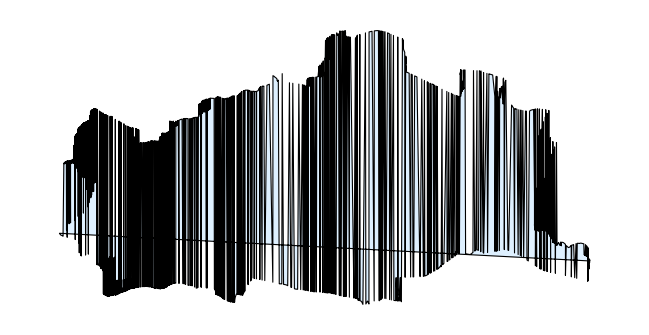

```mathematica
Graphics[{EdgeForm[Black],LightBlue, FromWKT[ToWKTerror[ply]]}]
```

```mathematica
file
```

{type→FeatureCollection,features→{{type→Feature,geometry→{type→Polygon,coordinates→{{{16.1818,48.1711},{16.1819,48.171},{16.1829,48.1698},{16.184,48.1693},{16.1842,48.1692},{16.1846,48.1689},{16.1877,48.1681},{16.1937,48.1664},{16.1962,48.164},{16.1974,48.1609},{16.1967,48.1566},{16.198,48.1545},{16.1982,48.1541},2351,{16.2039,48.194},{16.2039,48.1939},{16.2031,48.1909},{16.1998,48.1862},{16.1959,48.1838},{16.1932,48.1806},{16.1902,48.1789},{16.1891,48.1782},{16.1878,48.1771},{16.1876,48.1739},{16.1872,48.1736},{16.1818,48.1711}}}},properties→{osm_id→-109166,admin_level→4,parents→-16239,name→Vienna,local_name→Wien,name_en→Vienna}}}}
 |  |  |  |